```mathematica
p=10;
```

```mathematica
s=0.05;
```

```mathematica
x0=0.5;
```

```mathematica
c=p-1+1/x0;
```

```mathematica
numeric=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x0},x[t],{t,0,Infinity},MaxSteps->50000]
```

NDSolve::mxst: Maximum number of 50000 steps reached at the point t == 1.39870350793305×10^24940.

{{x[t]→InterpolatingFunction[{{0.,1.39870350793305×10^24940}},<>][t]}}

```mathematica
xappr[t_]:=1/(c*Exp[s*t]-p+1);
```

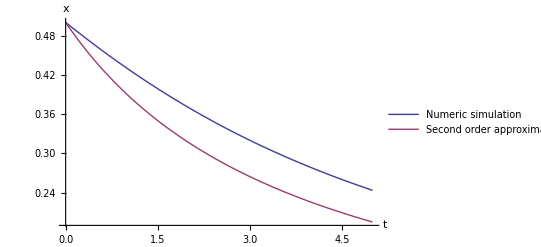

```mathematica
Plot[{Evaluate[x[t]/.numeric],Evaluate[xappr[t]]},{t,0,5},PlotLegends->Placed[{"Numeric simulation","Second order approximation"},{0.65,0.8}],AxesLabel->{"t","x"}]
```